# Report Project 1

Course code: IX1500
Date: 2020-09-08

Simon Johannesson, sijohann@kth.se
William Asp, wasp@kth.se

Probability experiment

## Summary

### Task

#### Task A

The task for pass grade for this project was to calculate the exact probability of common hands from a designated deck of cards. A hand is five cards. The hands to calculate were:

one pair

two pairs

three of a kind

four of a kind

full house

straight

flush

straight flush

The deck consisted of 10 black, 9 red, 8 green and 7 blue cards, 4 different types of card. To calculate the probability of the hands, the "census method" described in the Project1 instruction notebook were supposed to be used.

#### Task B

Verify the probability of full house and three of a kind that was the result of the census. Verify against given probability calculated by combinatorial calculus. Verify at least two other probabilities by combinatorial calculus. For the second part the probabilities for four of a kind, flush and straight flush were chosen.

#### Task C

Estimate the probability of getting pair or flush by using the Monte Carlo method.

### Result

#### a) Using census to calculate probability

Probability to get:

A pair			 139160/278256 ≈ 50.012%

Two pairs		 24321/278256 ≈ 8.741%

Three of a kind	 11482/278256≈ 4.126%

Four of a kind		 210/278256 ≈ 0.075%

Full house		 1163/278256 ≈ 0.418%

Straight		 1436/278256 ≈ 0.516%

Flush			 437/278256 ≈ 0.157%

Straight flush		 18/278256 ≈ 0.006%

#### b) Verifying census with with combinatorial calculus

Calculations of the probabilities for three of a kind, full house, four of a kind, flush and straight flush were consistent with the census. The probabilities are considered verified.

#### c) Estimate probability of a pair or a flush using the Monte Carlo Method

During one simulation of choosing 30 000 hands the probability of a pair was estimated to 50.04 %, and the probability of a flush was estimated to 0.15 %. Well in line with the probability calculated using census.

Number of hands chosen on random: 30 000
Number of hands with pair: 15 012
Number of hands with flush: 45

## Calculations

### Equations

#### Calculating probability

The formula for probability is calculated by P=(Number of outcomes)/(Total number of possibilities).
So, to calculate the number of outcomes for each case, a special function for each case was made to check if the criteria (a pair, two pairs etc.) is met for every subset of hands in the deck.

The probability for each case was then calculated by dividing the number of occurring cases, by the total number of subsets of hands.

For example:
P_straight=N_straight/N_tot=1436/278256≈0.516%
The probability of getting a straight is the number of times a straight hand occurs N_straight divided by the total amount of hands N_tot. Here the result is that the probability to get a straight hand is 0.516%.

#### Verifying probabilities by combinatorial calculus

##### Verifying census for full hand and three of a kind

The census provided the probability for three of a kind:

P_threeOfAKindCensus=n_threeOfAKindCensus/n=11482/278256= 5741/139128≈0.0412642

Which is the same as the probability received when calculating it with combinatorial calculus.

P_(three of a kindCombinatorial)=(n_(three of a kindCombinatorial))/n=11482/278256=5741/139128≈0.0412642

P_threeOfAKindCensus=P_(three of a kindCombinatorial)

The census provided the probability for full hand:

P_fullHouseCensus=n_fullHouseCensus/n=1163/278256≈0.0041796

Which is the same as the probability received when calculating it with combinatorial calculus.

P_(full houseCombinatorial)=(n_(full houseCombinatorial))/n=1163/278256≈0.0041796

P_fullHouseCensus=P_(full houseCombinatorial)

##### Verifying census for four of a kind, flush and straight flush

Calculating the probability for four of a kind

To calculate the amount of hands that have a four of a kind first remove the four cards from the deck, and then calculate how many different possible hands can be generated with the one card that is left, in other words (30
1), note that there are 34 cards in the deck from the beginning. This result must then  be multiplied with 7 since there are 7 different possible combination of four cards that can generate four of a kind.

n_fourOfAKindCombinatorial = 7 (30
1) = 210

P_fourOfAKindCombinatorial=n_fourOfAKindCombinatorial/n=210/278256≈0.000754701

The census provided the probability as below:

n_fourOfAKindCensus = 210
P_fourOfAKindCensus=n_fourOfAKindCensus/n=210/278256≈0.000754701

Which coincides with the result from the combinatorial calculation.

P_fourOfAKindCombinatorial= P_fourOfAKindCensus

Calculating the probability for flush (and straight flush)

To determine the number of ways to get a flush, first determine how many ways it is possible to choose 5 cards from each color. In this case we have colors with 10, 9, 8 and 7 cards. So in total there will be (10
5)+(9
5)+(8
5)+(7
5) ways to pick out a hand with all the same colors. However, this will include hands that are straight flushes. So these must be calculated and removed. To pick an ordered set of 5 from a set of 10 only has 6 possibilities. From a set of 9, 5 possibilities. From a set of 8, 4 possibilities. From a set of 7, 3 possibilities. Then we have also calculated the possibilities of getting a straight flush.

n_straightFlushCombinatorial = 6+5+4+3= 18

n_flushCombinatorial = (10
5)-6+(9
5)-5+(8
5)-4+(7
5)-3 = 437

P_straightFlushCombinatorial=n_straightFlushCombinatorial/n=18/278256=3/46376≈0.0000646886

P_flushCombinatorial=n_flushCombinatorial/n=437/278256≈0.0015705

The census provided the probability for getting a straight flush and a flush as below:

P_straightFlushCensus=n_straightFlushCensus/n=18/278256=3/46376≈0.0000646886

P_flushCensus=n_flushCensus/n=437/278256≈0.0015705

Which coincides with the results when calculating the probability using combinatorial calculus.

P_straightFlushCombinatorial= P_straightFlushCensus
P_flushCombinatorial= P_flushCensus

### Discussion

#### Task A

The result we got feels reasonable, because since we do not rely on any advanced formulas, we rely on the computer to count the number of times a special hand occurs in the total amount of hands. In turn, this makes the weak link our functions that define how a hand is interpreted. Through an analysis of each function one can be rather certain that it should produce the correct output.

#### Task B

#### Task C

### Diagrams

Diagrams of two outcomes from the Monte Carlo method.

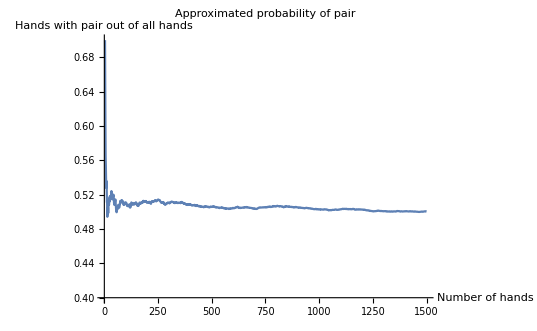
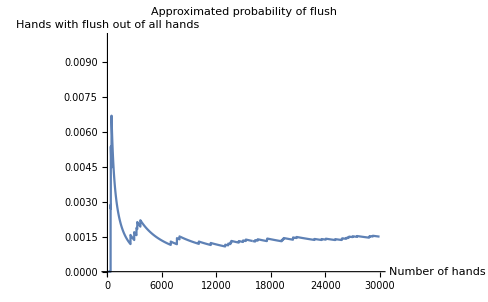

### Conclusion

#### Task A

To calculate the probability for a large problem, sometimes, a good solution is to let the computer do the counting, and the problem to solve then is to give the computer the right instructions.

#### Task B

#### Task C

## Code

The code should be run sequentially in order to function properly.

#### Calculating probability of hands:

```mathematica
ClearAll["`*"]
```

Alternate representation of cards in the deck.

```mathematica
cards = {
101, 102, 103, 104, 105,106, 107, 108, 109,110,
201, 202, 203, 204,205,206,207,208,209,
301,302,303,304,305,306,307, 308,
401,402,403,404,405,406,407
};
```

```mathematica
getCardValuesH[hand_] :=Sort[Mod[hand,100]]
```

```mathematica
getCardColorsH[hand_] := Sort[Quotient[hand,100]]
```

```mathematica
pairH[{___, x_, x_,___,y_,y_,___} /;x≠ y]:= False;
pairH[{___, x_, x_, x_,___}]:= False;
pairH[{___, x_, x_,___}]:= True;
pairH[{___}]:= False;
pairQ[hand_]:= pairH[getCardValuesH[hand]]
```

```mathematica
twoPairH[{___, x_,x_,x_,___}]:= False;
twoPairH[{___}]:=False;
twoPairH[{___, x_, x_,___, y_,y_,___} /;x≠ y]:= True;
twoPairQ[hand_]:= twoPairH[getCardValuesH[hand]];
```

```mathematica
threeOfAKindH[{___,x_,x_,x_,x_,___}]:=False;
threeOfAKindH[{x_,x_,x_,y_, y_}]/; x≠y:= False;
threeOfAKindH[{x_,x_,y_,y_, y_}]/; x≠y:= False;
threeOfAKindH[{___,x_,x_,x_,___}]:=True;
threeOfAKindH[{___}]:= False;
threeOfAKindQ[hand_]:= threeOfAKindH[getCardValuesH[hand]]
```

```mathematica
fourOfAKindH[{___,x_,x_,x_,x_,___}]:=True;
fourOfAKindH[{___}]:=False;
fourOfAKindQ[hand_]:=fourOfAKindH[getCardValuesH[hand]]
```

```mathematica
fullHouseH[{x_,x_,x_,y_, y_}]:=True;
fullHouseH[{x_,x_,y_,y_, y_}]:=True;
fullHouseH[{___}]:= False;
fullHouseQ[hand_]:= fullHouseH[getCardValuesH[hand]]
```

```mathematica
straightQ[hand_]:=Not[straightFlushQ[hand]]&&Sort[Mod[hand,100]]-Mod[Sort[hand][[1]],100]=={0,1,2,3,4};
straightFlushQ[hand_]:=Sort[hand]-Sort[hand]⟦1⟧=={0,1,2,3,4};
flushQ[hand_]:= Not[straightFlushQ[hand]] && Equal@@ Quotient[hand,100];
```

```mathematica
subsets = Subsets[cards, {5}];
```

```mathematica
numSubsets = Length[subsets];
numStraightFlush = Count[subsets, _?straightFlushQ];
numFlush = Count[subsets, _?flushQ];
numStraight = Count[subsets, _?straightQ];
numOnePair = Count[subsets, _?pairQ];
numTwoPair = Count[subsets, _?twoPairQ];
numThreeOfAKind = Count[subsets, _?threeOfAKindQ];
numFourOfAKind = Count[subsets, _?fourOfAKindQ];
numFullHouse = Count[subsets, _?fullHouseQ];
probability[x_]:= x/numSubsets;
probabilityOnePair = probability[numOnePair];
probabilityTwoPair = probability[numTwoPair];
probabilityThreeOfAKind = probability[numThreeOfAKind];
probabilityFourOfAKind = probability[numFourOfAKind];
probabilityFullHouse = probability[numFullHouse];
probabilityFlush = probability[numFlush];
probabilityStraight = probability[numStraight];
probabilityStraightFlush = probability[numStraightFlush];
```

```mathematica
N[probabilityOnePair ]*100
```

50.0115

```mathematica
N[probabilityTwoPair ]*100
```

8.74051

```mathematica
N[probabilityThreeOfAKind ]*100
```

4.12642

```mathematica
N[probabilityFourOfAKind ]*100
```

0.0754701

```mathematica
N[probabilityFullHouse ]*100
```

0.41796

```mathematica
N[probabilityFlush ]*100
```

0.15705

```mathematica
N[probabilityStraight ]*100
```

0.516072

```mathematica
N[probabilityStraightFlush ]*100
```

0.00646886

#### Tests below:

```mathematica
pair = {201, 301, 205,206,207};
twoPair = {201, 301, 205,405,207};
threeOfAKind = {201, 302, 205,405,305};
fullHouse = {201, 301, 205,405,305};
fourOfAKind = {105, 301, 205,405,305};
flush = { 201, 203, 205,206,207};
straight = {104,305,206,407, 308};
straightFlush = {403,404,405,406,407};
twoPairB = {201, 301, 502,603, 703};
```

```mathematica
pairQ[pair]
pairQ[twoPair]
pairQ[threeOfAKind]
pairQ[fourOfAKind]
pairQ[fullHouse]
pairQ[twoPairB]
```

True

False

False

False

«2 more identical outputs»

```mathematica
twoPairQ[pair]
twoPairQ[twoPair]
twoPairQ[threeOfAKind]
twoPairQ[fourOfAKind]
twoPairQ[fullHouse]
twoPairQ[twoPairB]
```

False

True

False

False

False

True

```mathematica
threeOfAKindQ[pair]
threeOfAKindQ[twoPair]
threeOfAKindQ[threeOfAKind]
threeOfAKindQ[fourOfAKind]
threeOfAKindQ[fullHouse]
```

False

False

True

False

False

```mathematica
fourOfAKindQ[pair]
fourOfAKindQ[twoPair]
fourOfAKindQ[threeOfAKind]
fourOfAKindQ[fourOfAKind]
fourOfAKindQ[fullHouse]
```

False

False

False

True

False

```mathematica
fullHouseQ[pair]
fullHouseQ[twoPair]
fullHouseQ[threeOfAKind]
fullHouseQ[fourOfAKind]
fullHouseQ[fullHouse]
```

False

False

False

«1 more identical outputs»

True

```mathematica
straightFlushQ[straightFlush]
straightFlushQ[flush]
straightFlushQ[straight]
```

True

False

False

```mathematica
flushQ[flush]
flushQ[straight]
flushQ[straightFlush]
```

True

False

False

```mathematica
straightQ[straight]
straightQ[flush]
straightQ[straightFlush]
```

True

False

False

#### Approximating probabilities with the Monte Carlo method

```mathematica
probability[hits_,n_]:= Divide[hits,n]; 
listOfProbabilitiesFlush = {};
listOfProbabilitiesPair = {};
checks = 0;
hitsForFlush = 0;
hitsForPair = 0;
n = 30000;
For[i =0, i<n,i++,
checks++;
hand = subsets[[RandomInteger[{1,Length[subsets]}]]];
If[pairQ[hand],
hitsForPair++;
,
If[flushQ[hand],
hitsForFlush++;
,
Nothing;
];
];
AppendTo[listOfProbabilitiesFlush, probability[hitsForFlush, checks]];
AppendTo[listOfProbabilitiesPair, 
probability[hitsForPair, checks]];
];
```

```mathematica
Print["Pairs:\nNumber of checks: ",checks , "\nHits pars: " , hitsForPair
 , "\nFinal probability: " ,N[Last[listOfProbabilitiesPair]] * 100 ," %" ]
Print["Flush:\nNumber of checks: " , checks , "\nHits flush: " , hitsForFlush , 
"\nFinal probability: " ,N[Last[listOfProbabilitiesFlush]] * 100 ," %" ]
```

When plotting the list with probabilities for pairs only every 20th element is used to clean up the plot a bit.

```mathematica
ListLinePlot[listOfProbabilitiesPair[[ ;;;;20]], PlotRange->{0.4,0.7}, PlotLabel->HoldForm[Approximated probability of pair],AxesLabel->{"Number of hands","Hands with pair out of all hands"}]
```

```mathematica
ListLinePlot[listOfProbabilitiesFlush, PlotRange->{0,0.01}, PlotLabel->HoldForm[Approximated probability of flush],AxesLabel->{"Number of hands","Hands with flush out of all hands"}]
```